```mathematica
z0=800*10^(-3); (*mm*)
lam = 5320*10^(-10); (*А*)
Object=50.0*10^(-3);
Xbeg=-Object/2.0;
Xend=Object/2.0;
SetDirectory[NotebookDirectory[]]
JK = Import["data/x_dPhi_range1e-05step2.5e-07scaling1diversity0.2blurry_x.txt", "Table"];
JKleft=Table[{-Object/2+(JK[[2,1]]-JK[[1,1]])*i, -Object/2+1000*(JK[[2,1]]-JK[[1,1]])*i, JK[[1,3]]},{i,0,(JK[[1,1]]-(-Object/2))/1000/(JK[[2,1]]-JK[[1,1]])-1,1}];
JKright=Table[{-JK[[1,1]]+(JK[[2,1]]-JK[[1,1]])*i, -JK[[1,1]]+1000*(JK[[2,1]]-JK[[1,1]])*i, JK[[Length[JK],3]]},{i,0,(JK[[1,1]]-(-Object/2))/1000/(JK[[2,1]]-JK[[1,1]]),1}];
HalfLeft=Table[{-Object/2+(JK[[2,1]]-JK[[1,1]])*i, -Object/2+1000*(JK[[2,1]]-JK[[1,1]])*i, JK[[1,3]]},{i,0,(0-Xbeg)/1000/(JK[[2,1]]-JK[[1,1]])-1,1}];

HalfRight=Table[{0+(JK[[2,1]]-JK[[1,1]])*i, -JK[[1,1]]+(JK[[2,1]]-JK[[1,1]])*i, JK[[Length[JK],3]]},{i,0,(JK[[1,1]]-(-Object/2))/(JK[[2,1]]-JK[[1,1]]),1}];WindowNS=Join[JKleft,JK,JKright];
WindowJump=Join[HalfLeft,HalfRight];
WindowHole=Join[JKleft,JKright];
WindowHole
```

/Users/mikhail/Diffraction

{{-0.025,-0.025,566914.},{-0.0249998,-0.02475,566914.},{-0.0249995,-0.0245,566914.},{-0.0249993,-0.02425,566914.},{-0.024999,-0.024,566914.},{-0.0249988,-0.02375,566914.},{-0.0249985,-0.0235,566914.},{-0.0249983,-0.02325,566914.},{-0.024998,-0.023,566914.},{-0.0249978,-0.02275,566914.},{-0.0249975,-0.0225,566914.},{-0.0249973,-0.02225,566914.},{-0.024997,-0.022,566914.},{-0.0249968,-0.02175,566914.},{-0.0249965,-0.0215,566914.},{-0.0249963,-0.02125,566914.},{-0.024996,-0.021,566914.},{-0.0249958,-0.02075,566914.},{-0.0249955,-0.0205,566914.},{-0.0249953,-0.02025,566914.},{-0.024995,-0.02,566914.},{-0.0249948,-0.01975,566914.},{-0.0249945,-0.0195,566914.},{-0.0249943,-0.01925,566914.},{-0.024994,-0.019,566914.},{-0.0249938,-0.01875,566914.},{-0.0249935,-0.0185,566914.},{-0.0249933,-0.01825,566914.},{-0.024993,-0.018,566914.},{-0.0249928,-0.01775,566914.},{-0.0249925,-0.0175,566914.},{-0.0249923,-0.01725,566914.},{-0.024992,-0.017,566914.},{-0.0249918,-0.01675,566914.},{-0.0249915,-0.0165,566914.},{-0.0249913,-0.01625,566914.},{-0.024991,-0.016,566914.},{-0.0249908,-0.01575,566914.},{-0.0249905,-0.0155,566914.},{-0.0249903,-0.01525,566914.},{-0.02499,-0.015,566914.},{-0.0249898,-0.01475,566914.},{-0.0249895,-0.0145,566914.},{-0.0249893,-0.01425,566914.},{-0.024989,-0.014,566914.},{-0.0249888,-0.01375,566914.},{-0.0249885,-0.0135,566914.},{-0.0249883,-0.01325,566914.},{-0.024988,-0.013,566914.},{-0.0249878,-0.01275,566914.},{-0.0249875,-0.0125,566914.},{-0.0249873,-0.01225,566914.},{-0.024987,-0.012,566914.},{-0.0249868,-0.01175,566914.},{-0.0249865,-0.0115,566914.},{-0.0249863,-0.01125,566914.},{-0.024986,-0.011,566914.},{-0.0249858,-0.01075,566914.},{-0.0249855,-0.0105,566914.},{-0.0249853,-0.01025,566914.},{-0.024985,-0.01,566914.},{-0.0249848,-0.00975,566914.},{-0.0249845,-0.0095,566914.},{-0.0249843,-0.00925,566914.},{-0.024984,-0.009,566914.},{-0.0249838,-0.00875,566914.},{-0.0249835,-0.0085,566914.},{-0.0249833,-0.00825,566914.},{-0.024983,-0.008,566914.},{-0.0249828,-0.00775,566914.},{-0.0249825,-0.0075,566914.},{-0.0249823,-0.00725,566914.},{-0.024982,-0.007,566914.},{-0.0249818,-0.00675,566914.},{-0.0249815,-0.0065,566914.},{-0.0249813,-0.00625,566914.},{-0.024981,-0.006,566914.},{-0.0249808,-0.00575,566914.},{-0.0249805,-0.0055,566914.},{-0.0249803,-0.00525,566914.},{-0.02498,-0.005,566914.},{-0.0249798,-0.00475,566914.},{-0.0249795,-0.0045,566914.},{-0.0249793,-0.00425,566914.},{-0.024979,-0.004,566914.},{-0.0249788,-0.00375,566914.},{-0.0249785,-0.0035,566914.},{-0.0249783,-0.00325,566914.},{-0.024978,-0.003,566914.},{-0.0249778,-0.00275,566914.},{-0.0249775,-0.0025,566914.},{-0.0249773,-0.00225,566914.},{-0.024977,-0.002,566914.},{-0.0249768,-0.00175,566914.},{-0.0249765,-0.0015,566914.},{-0.0249763,-0.00125,566914.},{-0.024976,-0.001,566914.},{-0.0249758,-0.00075,566914.},{-0.0249755,-0.0005,566914.},{0.00001,0.00001,566918.},{0.00001025,0.00026,566918.},{0.0000105,0.00051,566918.},{0.00001075,0.00076,566918.},{0.000011,0.00101,566918.},{0.00001125,0.00126,566918.},{0.0000115,0.00151,566918.},{0.00001175,0.00176,566918.},{0.000012,0.00201,566918.},{0.00001225,0.00226,566918.},{0.0000125,0.00251,566918.},{0.00001275,0.00276,566918.},{0.000013,0.00301,566918.},{0.00001325,0.00326,566918.},{0.0000135,0.00351,566918.},{0.00001375,0.00376,566918.},{0.000014,0.00401,566918.},{0.00001425,0.00426,566918.},{0.0000145,0.00451,566918.},{0.00001475,0.00476,566918.},{0.000015,0.00501,566918.},{0.00001525,0.00526,566918.},{0.0000155,0.00551,566918.},{0.00001575,0.00576,566918.},{0.000016,0.00601,566918.},{0.00001625,0.00626,566918.},{0.0000165,0.00651,566918.},{0.00001675,0.00676,566918.},{0.000017,0.00701,566918.},{0.00001725,0.00726,566918.},{0.0000175,0.00751,566918.},{0.00001775,0.00776,566918.},{0.000018,0.00801,566918.},{0.00001825,0.00826,566918.},{0.0000185,0.00851,566918.},{0.00001875,0.00876,566918.},{0.000019,0.00901,566918.},{0.00001925,0.00926,566918.},{0.0000195,0.00951,566918.},{0.00001975,0.00976,566918.},{0.00002,0.01001,566918.},{0.00002025,0.01026,566918.},{0.0000205,0.01051,566918.},{0.00002075,0.01076,566918.},{0.000021,0.01101,566918.},{0.00002125,0.01126,566918.},{0.0000215,0.01151,566918.},{0.00002175,0.01176,566918.},{0.000022,0.01201,566918.},{0.00002225,0.01226,566918.},{0.0000225,0.01251,566918.},{0.00002275,0.01276,566918.},{0.000023,0.01301,566918.},{0.00002325,0.01326,566918.},{0.0000235,0.01351,566918.},{0.00002375,0.01376,566918.},{0.000024,0.01401,566918.},{0.00002425,0.01426,566918.},{0.0000245,0.01451,566918.},{0.00002475,0.01476,566918.},{0.000025,0.01501,566918.},{0.00002525,0.01526,566918.},{0.0000255,0.01551,566918.},{0.00002575,0.01576,566918.},{0.000026,0.01601,566918.},{0.00002625,0.01626,566918.},{0.0000265,0.01651,566918.},{0.00002675,0.01676,566918.},{0.000027,0.01701,566918.},{0.00002725,0.01726,566918.},{0.0000275,0.01751,566918.},{0.00002775,0.01776,566918.},{0.000028,0.01801,566918.},{0.00002825,0.01826,566918.},{0.0000285,0.01851,566918.},{0.00002875,0.01876,566918.},{0.000029,0.01901,566918.},{0.00002925,0.01926,566918.},{0.0000295,0.01951,566918.},{0.00002975,0.01976,566918.},{0.00003,0.02001,566918.},{0.00003025,0.02026,566918.},{0.0000305,0.02051,566918.},{0.00003075,0.02076,566918.},{0.000031,0.02101,566918.},{0.00003125,0.02126,566918.},{0.0000315,0.02151,566918.},{0.00003175,0.02176,566918.},{0.000032,0.02201,566918.},{0.00003225,0.02226,566918.},{0.0000325,0.02251,566918.},{0.00003275,0.02276,566918.},{0.000033,0.02301,566918.},{0.00003325,0.02326,566918.},{0.0000335,0.02351,566918.},{0.00003375,0.02376,566918.},{0.000034,0.02401,566918.},{0.00003425,0.02426,566918.},{0.0000345,0.02451,566918.},{0.00003475,0.02476,566918.}}

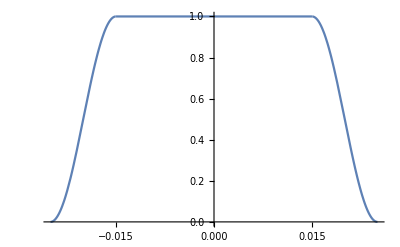

```mathematica
A[xw_]:=If[(xw-Xbeg)≤10.0*10^(-3),Sin[Pi/2/(10*10^(-3))*(xw-Xbeg)]^2,If[(xw-Xbeg)≥(Object-10.0*10^(-3)),Sin[Pi/2/(10*10^(-3))*((xw-Xbeg)-Object)]^2,1.0]];
Plot[A[x],{x,Xbeg,Xend},PlotRange->Full]
```

```mathematica
x[j_]:=WindowNS[[j,2]];
dPhi[j_]:=WindowNS[[j,3]];
r[j_,xp_]:=Sqrt[z0*z0+(x[j]-xp)*(x[j]-xp)];
steps = Length[WindowNS];
ResultNS[xp_]:=Sum[A[x[j]]*(z0/r[j,xp])^0.5*Exp[2*I*Pi / lam * (r[j,xp]-z0)+I*dPhi[j]], {j,1, steps}];
NExperimentNS=Table[{xp,Re[ResultNS[xp]*Conjugate[ResultNS[xp]]]},{xp,-6.0*10^(-3),6.0*10^(-3),0.02*10^(-3)}];
toStr[{x_,y_}]:=ToString[x]<>" "<>ToString[y]<>"\n"
WriteString[OpenWrite["data/NS_range1e-05step2.5e-07scaling1diversity0.2blurry_x.out"],StringJoin[toStr/@NExperimentNS]];
```

```mathematica
x[j_]:=WindowJump[[j,2]];
dPhi[j_]:=WindowJump[[j,3]];
r[j_,xp_]:=Sqrt[z0*z0+(x[j]-xp)*(x[j]-xp)];
steps = Length[WindowJump];
ResultJump[xp_]:=Sum[A[x[j]]*(z0/r[j,xp])^0.5*Exp[2*I*Pi / lam * (r[j,xp]-z0)+I*dPhi[j]], {j,1, steps}];
NExperimentJump=Table[{xp,Re[ResultJump[xp]*Conjugate[ResultJump[xp]]]},{xp,-6.0*10^(-3),6.0*10^(-3),0.02*10^(-3)}];
toStr[{x_,y_}]:=ToString[x]<>" "<>ToString[y]<>"\n"
WriteString[OpenWrite["data/Jump_range1e-05step2.5e-07scaling1diversity0.2blurry_x.out"],StringJoin[toStr/@NExperimentJump]];
```

$Aborted

StringJoin::string: String expected at position 1 in StringJoin[NExperimentJump].

```mathematica
x[j_]:=WindowHole[[j,2]];
dPhi[j_]:=WindowHole[[j,3]];
r[j_,xp_]:=Sqrt[z0*z0+(x[j]-xp)*(x[j]-xp)];
steps = Length[WindowHole];
ResultNS[xp_]:=Sum[A[x[j]]*(z0/r[j,xp])^0.5*Exp[2*I*Pi / lam * (r[j,xp]-z0)+I*dPhi[j]], {j,1, steps}];
NExperimentNS=Table[{xp,Re[ResultNS[xp]*Conjugate[ResultNS[xp]]]},{xp,-6.0*10^(-3),6.0*10^(-3),0.02*10^(-3)}];
toStr[{x_,y_}]:=ToString[x]<>" "<>ToString[y]<>"\n"
WriteString[OpenWrite["data/Hole_range1e-05step2.5e-07scaling1diversity0.2blurry_x.out"],StringJoin[toStr/@NExperimentNS]];
```

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

OpenWrite::noopen: Cannot open data/Hole_range1e-05step2.5e-07scaling1diversity0.2blurry_x.out.

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.